## Testing the effectiveness of ZPS in mitigating errors for one - loss cat code

M . Bergmann and P . van Loock, PRA 94, 042332 (2016)

```mathematica
𝒜:=1/(2 Cosh[T α^2]);

p0 := 𝒜 Cosh[γ T α^2](Cosh[(1-γ)T α^2]+Cos[(1-γ)T α^2]) ;
p1 := 𝒜 Sinh[γ T α^2](Sinh[(1-γ)T α^2]+Sin[(1-γ)T α^2]) ;
p2 := 𝒜 Cosh[γ T α^2](Cosh[(1-γ)T α^2]-Cos[(1-γ)T α^2]) ;
p3 := 𝒜 Sinh[γ T α^2](Sinh[(1-γ)T α^2]-Sin[(1-γ)T α^2]) ;

𝒩:=1/(1+2Re[a b*] Cos[T α^2]/Cosh[T α^2]);

p0Tilde[a_,b_,α_,T_,γ_] = 𝒩  p0 (1+2 Re[a b*] Cos[γ T α^2]/Cosh[γ T α^2]);
p1Tilde[a_,b_,α_,T_,γ_] = 𝒩  p1 (1-2 Re[a b*] Sin[γ T α^2]/Sinh[γ T α^2]);
p2Tilde[a_,b_,α_,T_,γ_] = 𝒩  p2 (1-2 Re[a b*] Cos[γ T α^2]/Cosh[γ T α^2]);
p3Tilde[a_,b_,α_,T_,γ_] = 𝒩  p3 (1+2 Re[a b*] Sin[γ T α^2]/Sinh[γ T α^2]);
```

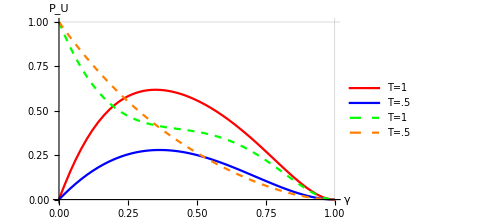

```mathematica
(* probability of uncorrectable errors *)
PU[a_,b_,α_,T_,γ_]=p2Tilde[a,b,α,T,γ]+p3Tilde[a,b,α,T,γ];

Module[{a,b,α,T1,T2,γ},
a=1/(√2);
b =a;
α = 2;
T1=1;
T2= .50;
Plot[{PU[a,b,α,T1,γ],PU[a,b,α,T2,γ],PU[a,-b,α,T1,γ],PU[a,-b,α,T2,γ]},{γ, 0,1},PlotRange->{0,1},AxesLabel->{"γ","P_U"},LabelStyle->{FontSize->20,FontFamily->"CMU Sans Serif",Black},AxesStyle->{{Thick,Black},{Thick,Black}},ImageSize->Medium,PlotStyle->{{Red,Thick},{Blue,Thick},{Green, Dashed,Thick},{Orange, Dashed,Thick}}, PlotLegends->{"T=1","T=.5","T=1","T=.5"},PlotRange->{{0,1},{0,1}},GridLines->{{1},{1}}]
]
```

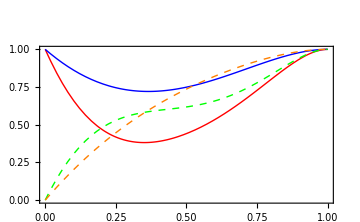

```mathematica
(* probability of correctable errors - including no error - this is just 1-PU*)
PC[a_,b_,α_,T_,γ_]=p0Tilde[a,b,α,T,γ]+p1Tilde[a,b,α,T,γ];

Module[{a,b,α,T1,T2,γ,plt,txt,text,xlab,ylab},
a=1/(√2);
b =a;
α = 2;
T1=1;
T2=.5;

text=Text[Style["a",{FontSize->35,FontFamily->"CMU Sans Serif",Black,Bold}],{.5,1.15},{0,0}];
txt=Graphics[{text}];

xlabel =Text[Style["γ",{FontSize->30,FontFamily->"CMU Sans Serif",Black}],{1.08,0},{0,0}];
xlab = Graphics[{xlabel}];

ylabel =Text[Style["P_C",{FontSize->30,FontFamily->"CMU Sans Serif",Black}],{0,1.12},{0,0}];
ylab = Graphics[{ylabel}];

plt = Plot[{PC[a,b,α,T1,γ],PC[a,b,α,T2,γ],PC[a,-b,α,T1,γ],PC[a,-b,α,T2,γ]},{γ, 0,1},PlotRange->{0,1},LabelStyle->{FontSize->20,FontFamily->"CMU Sans Serif",Black},FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},ImageSize->Medium,PlotStyle->{{Red,Thick},{Blue,Thick},{Green, Dashed,Thick},{Orange, Dashed,Thick}},PlotRange->All,Frame->True,PlotRangeClipping->False,ImagePadding->{{30, 35}, {30, 45}},PlotRangePadding->None];

Show[{plt, txt,xlab,ylab}]
]
```

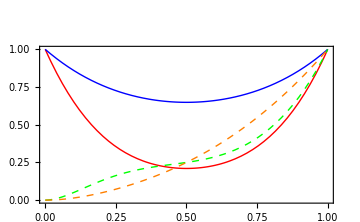

```mathematica
(* probability of mitigation *)
PM[a_,b_,α_,T_,γ_]=p0Tilde[a,b,α,T,γ];

Module[{a,b,α,T1,T2,γ,plt,txt,text,xlab,ylab},
a=1/(√2);
b =a;
α = 2;
T1=1;
T2=.5;

text=Text[Style["b",{FontSize->35,FontFamily->"CMU Sans Serif",Black,Bold}],{.5,1.15},{0,0}];
txt=Graphics[{text}];

xlabel =Text[Style["γ",{FontSize->30,FontFamily->"CMU Sans Serif",Black}],{1.08,0},{0,0}];
xlab = Graphics[{xlabel}];

ylabel =Text[Style["P_M",{FontSize->30,FontFamily->"CMU Sans Serif",Black}],{0,1.12},{0,0}];
ylab = Graphics[{ylabel}];

plt = Plot[{PM[a,b,α,T1,γ],PM[a,b,α,T2,γ],PM[a,-b,α,T1,γ],PM[a,-b,α,T2,γ]},{γ, 0,1},PlotRange->{0,1},LabelStyle->{FontSize->20,FontFamily->"CMU Sans Serif",Black},FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},ImageSize->Medium,PlotStyle->{{Red,Thick},{Blue,Thick},{Green, Dashed,Thick},{Orange, Dashed,Thick}},PlotRange->All,Frame->True,PlotRangeClipping->False,ImagePadding->{{30, 35}, {30, 45}},PlotRangePadding->None];

Show[{plt, txt,xlab,ylab}]
]
```

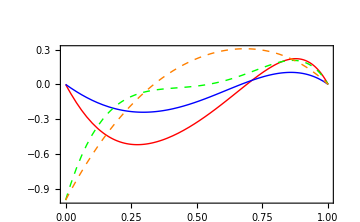

```mathematica
(* difference in probabilities of truly correctable errors v. uncorrectable errors *)
diff[a_,b_,α_,T_,γ_]=p1Tilde[a,b,α,T,γ]-PU[a,b,α,T,γ] ;

Module[{a,b,α,T1,T2,γ,plt,txt,text,xlab,ylab},
a=1/(√2);
b =a;
α = 2;
T1=1;
T2=.5;

text=Text[Style["c",{FontSize->35,FontFamily->"CMU Sans Serif",Black,Bold}],{.5,.5},{0,0}];
txt=Graphics[{text}];

xlabel =Text[Style["γ",{FontSize->30,FontFamily->"CMU Sans Serif",Black}],{1.08,-1},{0,0}];
xlab = Graphics[{xlabel}];

ylabel =Text[Style["(p̃)_1-P_U",{FontSize->30,FontFamily->"CMU Sans Serif",Black}],{.05,0.48},{0,0}];
ylab = Graphics[{ylabel}];

plt = Plot[{diff[a,b,α,T1,γ],diff[a,b,α,T2,γ],diff[a,-b,α,T1,γ],diff[a,-b,α,T2,γ]},{γ, 0,1},PlotRange->Full,LabelStyle->{FontSize->20,FontFamily->"CMU Sans Serif",Black},FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},ImageSize->Medium,PlotStyle->{{Red,Thick},{Blue,Thick},{Green, Dashed,Thick},{Orange, Dashed,Thick}},PlotRange->All,Frame->True,PlotRangeClipping->False,ImagePadding->{{30, 35}, {30, 45}},PlotRangePadding->None];

Show[{plt, txt,xlab,ylab}]
]
```

## Noisy ZPS vs noise after ideal ZPS

Input is an even two-component cat, of the form μ̄= 𝒩_+(ⅈ^μ α+-ⅈ^μα)

```mathematica
(* noisy ZPS *)

pLnoisyZPS[α_,T_,η_]=(Cosh[T α^2]Cosh[(1-η)(1-T)α^2])/Cosh[(1-η(1-T))α^2] ; (* probaility to stay logical *)
pEnoisyZPS[α_,T_,η_]=1-pLnoisyZPS[α,T,η] ;(* probaility of an error *)

(* ZPS then loss *)

pLZPSloss[β_,γ_]=pLnoisyZPS[β,γ,0] ; (* probaility to stay logical *)
pEZPSloss[β_,γ_]=1-pLnoisyZPS[β,γ,0] ;(* probaility of an error *)
```

```mathematica
(* Plot *)
cols=Reverse[RGBColor/@{(*"#053061","#2166ac",*)"#4393c3","#92c5de","#d1e5f0","#f7f7f7","#fddbc7","#f4a582","#d6604d"(*,"#b2182b","#67001f"*)}];
Manipulate[DensityPlot[HeavisideTheta[pLnoisyZPS[α ,T,0]-pLZPSloss[√(T/γ)α ,γ]],{T,0,1},{γ,0,1},ColorFunction->(Blend[cols,#]&),ColorFunctionScaling->True,FrameLabel->Automatic,LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},ImageSize->Medium],{α,1,4}]
```

General::munfl: Sech[1001.] is too small to represent as a normalized machine number; precision may be lost.

1.15393

```mathematica
Simplify[pLnoisyZPS[α ,T,0]-pLZPSloss[α,γ],γ==T]
```

0

```mathematica
Simplify[pLZPSloss[α,T]-pLnoisyZPS[α,γ,0],γ==T]
```

0

```mathematica
Simplify[pLnoisyZPS[α,γ,0]-pLZPSloss[α,T],γ==T]
```

0

```mathematica
pLnoisyZPS[α,γ,0]
```

Cosh[α^2 (1-γ)] Cosh[α^2 γ] Sech[α^2]